{0.,5.32907×10^-15,1.7053×10^-13,1.81899×10^-12,2.18279×10^-11,2.32831×10^-10,2.32831×10^-9,7.45058×10^-9,4.47035×10^-8,2.08616×10^-7,7.15256×10^-7,2.38419×10^-6,0.0000114441,0.0000228882,0.000106812,0.000244141,0.000854492,0.00244141,0.00683594,0.0214844,0.0390625,0.0625,0.1875,0.625,1.,4.,11.,30.,48.,80.,144.,256.,384.}

{0.,4.55295×10^-16,6.46234×10^-15,5.09954×10^-14,1.10024×10^-13,2.47286×10^-14,2.84763×10^-14,3.90373×10^-14,5.41333×10^-14,2.96249×10^-14,4.28295×10^-14,6.69888×10^-14,5.1472×10^-13,7.71813×10^-13,3.57142×10^-13,1.13405×10^-13,6.75299×10^-14,5.14938×10^-14,1.32587×10^-13,3.55196×10^-14,1.53133×10^-13,2.63143×10^-13,5.91795×10^-14,8.27125×10^-14,2.84039×10^-14,1.10766×10^-13,1.96238×10^-14,4.87433×10^-14,2.21036×10^-13,2.98044×10^-14,1.48962×10^-14,4.26949×10^-13,1.61973×10^-14}

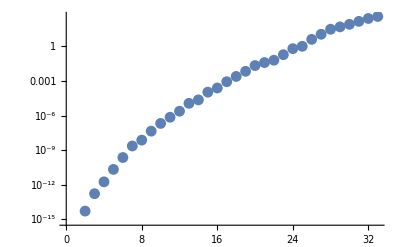

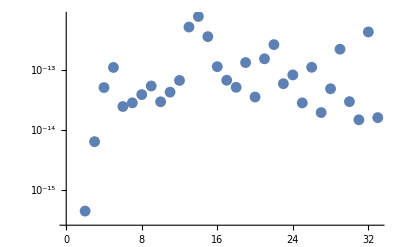

```mathematica
l = 31;
data = Import["jacobi_poly_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=JacobiP[k,-1/2,-1/2+m,y];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0.,1.42109×10^-14,1.7053×10^-13,1.36424×10^-12,3.63798×10^-12,1.81899×10^-11,5.82077×10^-11,1.45519×10^-10,2.32831×10^-10,4.65661×10^-10,1.39698×10^-9,3.72529×10^-9,5.58794×10^-9,1.49012×10^-8,2.98023×10^-8,5.96046×10^-8,7.45058×10^-8,1.49012×10^-7,4.17233×10^-7,7.15256×10^-7,1.19209×10^-6,1.66893×10^-6,4.29153×10^-6,8.10623×10^-6,0.0000138283,0.0000219345,0.0000314713,0.0000476837,0.0000572205,0.0000762939,0.000087738,0.0001297}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,0.,4.30526×10^-16,2.19767×10^-15,1.13634×10^-14,1.48392×10^-14,2.89999×10^-14,2.26829×10^-13,6.30159×10^-14,2.74667×10^-14,1.58479×10^-14,7.86443×10^-14,2.16358×10^-13,1.95238×10^-14,1.84272×10^-14,5.4993×10^-14,6.80612×10^-14,1.03611×10^-13,1.39349×10^-13,5.50726×10^-14,4.0696×10^-14,1.3461×10^-13,1.32087×10^-13,7.8462×10^-14,3.55667×10^-13,3.70138×10^-13,8.81845×10^-14,7.20403×10^-13,7.23228×10^-14,4.02889×10^-14,4.47754×10^-14,4.51958×10^-14,5.425×10^-14}

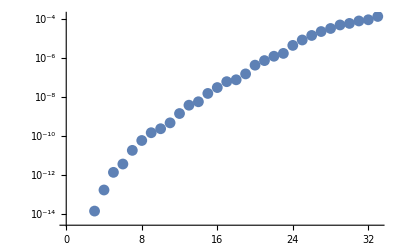

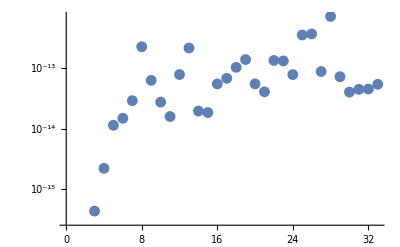

```mathematica
l = 10;
data = Import["jacobi_diff_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-1<0,0,1/2 (m+k) JacobiP[-1+k,1/2,1/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0,0.,1.7053×10^-13,1.81899×10^-12,1.09139×10^-11,5.82077×10^-11,2.32831×10^-10,6.98492×10^-10,2.79397×10^-9,7.45058×10^-9,1.49012×10^-8,3.72529×10^-8,1.04308×10^-7,2.68221×10^-7,4.17233×10^-7,8.34465×10^-7,1.66893×10^-6,3.8147×10^-6,9.53674×10^-6,0.0000162125,0.0000324249,0.0000457764,0.0000610352,0.00012207,0.000213623,0.000366211,0.000549316,0.0010376,0.00183105,0.00366211,0.00488281,0.00683594}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,0.,4.09003×10^-16,6.34952×10^-15,2.21807×10^-14,5.36502×10^-15,1.45121×10^-14,4.58881×10^-14,6.87154×10^-15,6.8732×10^-14,2.04508×10^-14,3.99775×10^-14,2.281×10^-14,7.07526×10^-15,1.15915×10^-14,2.11719×10^-14,4.66972×10^-14,1.25285×10^-13,1.48423×10^-13,7.0781×10^-14,7.3482×10^-14,2.92462×10^-14,6.98932×10^-13,5.63402×10^-13,1.7509×10^-13,1.03446×10^-13,3.6274×10^-14,1.54035×10^-13,1.03801×10^-13,3.56265×10^-14,4.9799×10^-14,5.04666×10^-14}

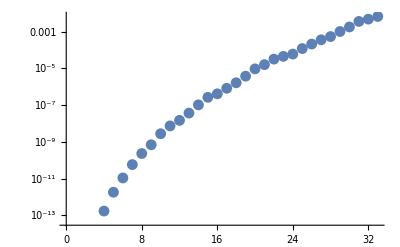

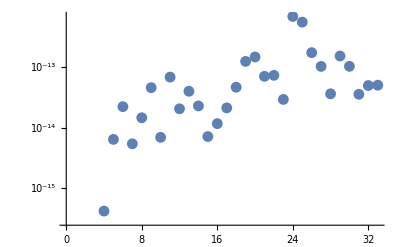

```mathematica
l = 10;
data = Import["jacobi_diff2_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-2<0,0,1/4 (k+m) (1+k+m) JacobiP[-2+k,3/2,3/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{0,0,0,0.,1.36424×10^-12,2.18279×10^-11,1.16415×10^-10,1.16415×10^-9,3.72529×10^-9,1.11759×10^-8,5.96046×10^-8,1.78814×10^-7,4.76837×10^-7,1.43051×10^-6,4.29153×10^-6,0.0000104904,0.0000133514,0.0000495911,0.0000991821,0.000183105,0.000457764,0.000854492,0.00170898,0.00280762,0.00488281,0.00976563,0.0205078,0.0332031,0.0507813,0.09375,0.164063,0.25,0.40625}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,0.,5.73988×10^-16,7.28341×10^-15,5.25507×10^-15,5.43533×10^-14,2.35109×10^-14,2.0558×10^-14,1.1022×10^-14,1.16522×10^-14,5.40969×10^-13,4.36877×10^-14,7.34461×10^-14,1.53037×10^-14,1.59961×10^-14,2.86061×10^-13,8.24875×10^-14,2.72538×10^-12,2.62548×10^-14,1.85991×10^-14,1.41848×10^-12,5.39712×10^-13,1.0597×10^-14,1.31196×10^-13,5.44088×10^-14,2.21479×10^-13,3.63626×10^-13,2.04314×10^-14,2.64431×10^-13,6.66658×10^-14,7.75974×10^-13}

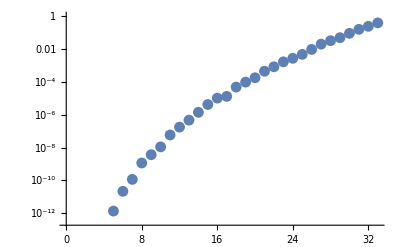

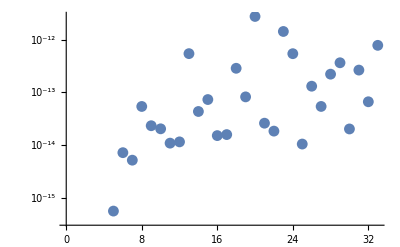

```mathematica
l = 10;
data = Import["jacobi_diff3_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=If[k-3<0,0,1/8 (k+m) (1+k+m) (2+k+m) JacobiP[-3+k,5/2,5/2+m,y]];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{3.33067×10^-16,3.33067×10^-16,3.33067×10^-16,3.88578×10^-16,6.10623×10^-16,7.49401×10^-16,8.88178×10^-16,9.99201×10^-16,1.08247×10^-15,1.22125×10^-15,1.33227×10^-15,1.58207×10^-15,1.77636×10^-15,1.9984×10^-15,2.13718×10^-15,2.27596×10^-15,2.41474×10^-15,2.6229×10^-15,2.7478×10^-15,2.84495×10^-15,2.9976×10^-15,3.17801×10^-15,3.4972×10^-15,3.76088×10^-15,3.95517×10^-15,4.14946×10^-15,4.31599×10^-15,4.48253×10^-15,4.67681×10^-15,4.8711×10^-15,5.1209×10^-15,5.3707×10^-15,5.57887×10^-15}

{3.77118×10^-15,4.20714×10^-15,5.03189×10^-15,4.34307×10^-14,6.0174×10^-15,2.4018×10^-14,4.12944×10^-14,1.70725×10^-14,3.39818×10^-14,1.34977×10^-13,8.88554×10^-14,3.62635×10^-14,8.57042×10^-14,1.81434×10^-14,3.26585×10^-14,4.07816×10^-14,1.93052×10^-14,9.20747×10^-14,1.16934×10^-11,4.67555×10^-14,2.8118×10^-14,4.69147×10^-14,1.04326×10^-13,5.04439×10^-14,4.31176×10^-14,4.46734×10^-13,5.06657×10^-14,5.46067×10^-14,2.34983×10^-13,1.83556×10^-13,6.97967×10^-14,7.60415×10^-14,1.5788×10^-13}

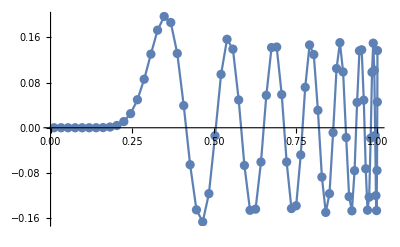

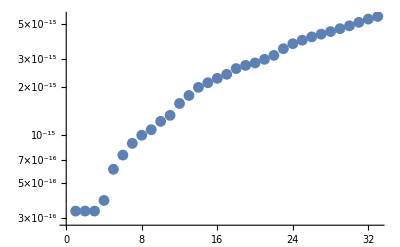

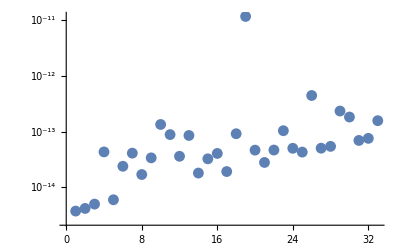

```mathematica
l = 13;
data = Import["worland_poly_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^m JacobiP[k,-1/2,m-1/2,2 y^2-1];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

{3.33067×10^-16,3.33067×10^-16,4.44089×10^-16,3.88578×10^-16,5.27356×10^-16,6.66134×10^-16,9.02056×10^-16,1.04777×10^-15,1.14492×10^-15,1.20563×10^-15,1.23339×10^-15,1.249×10^-15,1.33227×10^-15,1.52656×10^-15,1.77636×10^-15,2.02616×10^-15,2.19269×10^-15,2.47025×10^-15,2.6229×10^-15,2.78944×10^-15,2.9976×10^-15,3.21965×10^-15,3.51108×10^-15,3.81639×10^-15,4.05231×10^-15,4.26048×10^-15,4.44089×10^-15,4.63518×10^-15,4.85723×10^-15,5.07927×10^-15,5.34295×10^-15,5.6205×10^-15,5.85643×10^-15}

{3.51313×10^-15,3.62106×10^-15,5.74423×10^-15,8.59186×10^-15,4.99194×10^-15,2.09865×10^-14,2.96682×10^-14,1.78765×10^-14,3.58903×10^-14,1.45682×10^-13,9.67558×10^-14,3.96777×10^-14,7.11563×10^-14,1.98847×10^-14,4.12289×10^-14,3.50358×10^-14,2.45612×10^-14,8.3608×10^-14,4.21039×10^-12,2.30442×10^-13,6.88828×10^-14,4.26691×10^-14,7.33089×10^-14,4.00855×10^-14,4.41741×10^-14,6.96372×10^-13,5.21289×10^-14,8.80107×10^-14,2.45164×10^-13,1.242×10^-13,7.28189×10^-14,7.95737×10^-14,3.23438×10^-13}

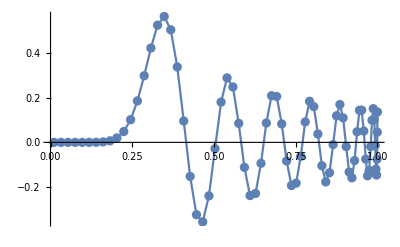

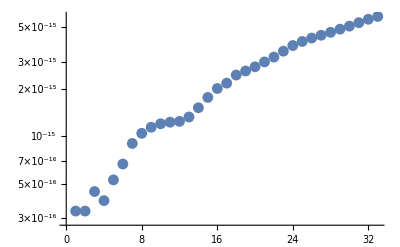

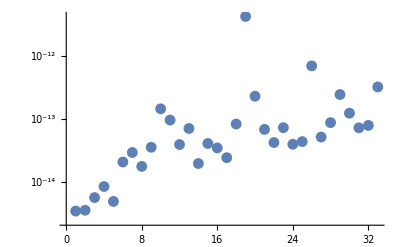

```mathematica
l = 13;
data = Import["worland_divr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^(m-1)JacobiP[k,-1/2,m-1/2,2 y^2-1];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
D[y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]
```

2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]

{7.10543×10^-15,1.06581×10^-14,1.77636×10^-14,2.84217×10^-14,7.10543×10^-14,1.13687×10^-13,2.27374×10^-13,2.98428×10^-13,3.69482×10^-13,4.40536×10^-13,5.11591×10^-13,6.82121×10^-13,7.10543×10^-13,8.66862×10^-13,1.10845×10^-12,1.19371×10^-12,1.39266×10^-12,1.44951×10^-12,1.67688×10^-12,1.67688×10^-12,1.64846×10^-12,1.6982×10^-12,1.71596×10^-12,1.69997×10^-12,1.66622×10^-12,1.61293×10^-12,1.53477×10^-12,1.59162×10^-12,1.87583×10^-12,2.10321×10^-12,2.72848×10^-12,3.24007×10^-12,3.63798×10^-12}

{3.19589×10^-15,2.20572×10^-14,3.44301×10^-15,5.24886×10^-15,1.02745×10^-13,2.20482×10^-14,5.26566×10^-14,7.69312×10^-15,7.87833×10^-15,2.34049×10^-13,8.20532×10^-15,6.86879×10^-14,1.92698×10^-14,2.08101×10^-13,3.57054×10^-14,1.46509×10^-13,5.32144×10^-14,7.48732×10^-14,4.16928×10^-14,2.87931×10^-14,3.78723×10^-14,8.25809×10^-13,1.77386×10^-13,3.41033×10^-13,1.86554×10^-13,7.96708×10^-13,8.80042×10^-14,3.64314×10^-13,1.03988×10^-13,4.05257×10^-14,1.77633×10^-14,1.93196×10^-13,5.48377×10^-14}

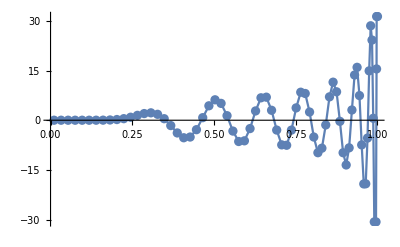

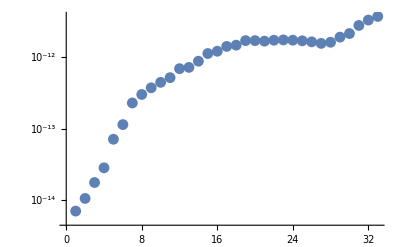

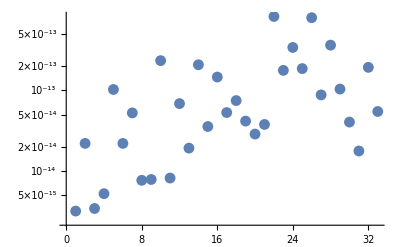

```mathematica
l = 13;
data = Import["worland_diff_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2];
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{8.88178×10^-15,7.10543×10^-15,1.77636×10^-14,2.4869×10^-14,5.68434×10^-14,1.42109×10^-13,2.55795×10^-13,3.55271×10^-13,4.40536×10^-13,4.9738×10^-13,5.25802×10^-13,5.96856×10^-13,7.10543×10^-13,8.10019×10^-13,9.52127×10^-13,1.00897×10^-12,1.06581×10^-12,1.12266×10^-12,1.19371×10^-12,1.25056×10^-12,1.28608×10^-12,1.3074×10^-12,1.81899×10^-12,2.16005×10^-12,2.44427×10^-12,2.84217×10^-12,3.24007×10^-12,3.9222×10^-12,4.3201×10^-12,4.718×10^-12,5.22959×10^-12,5.79803×10^-12,6.30962×10^-12}

{4.05639×10^-15,3.90669×10^-15,1.3308×10^-14,4.92839×10^-15,3.73031×10^-14,3.72394×10^-14,2.28651×10^-14,2.14443×10^-14,1.65075×10^-13,2.67846×10^-14,2.61637×10^-14,2.52149×10^-14,1.33386×10^-14,4.22533×10^-14,5.75245×10^-14,1.82967×10^-13,1.44735×10^-13,2.68965×10^-14,5.8516×10^-14,4.03925×10^-14,3.84689×10^-14,8.8272×10^-14,3.90141×10^-13,2.59657×10^-13,6.5296×10^-13,4.95168×10^-14,5.36561×10^-13,7.44049×10^-14,8.48031×10^-14,1.63673×10^-14,3.50622×10^-14,2.14346×10^-13,9.09288×10^-14}

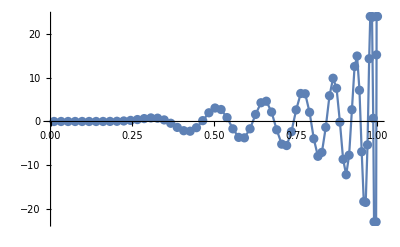

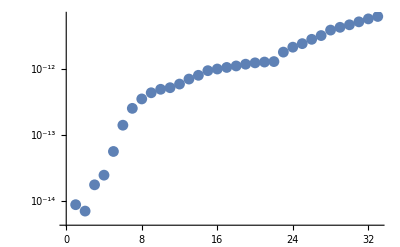

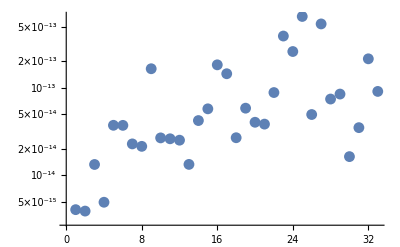

```mathematica
l = 13;
data = Import["worland_diffr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{8.88178×10^-15,1.42109×10^-14,2.84217×10^-14,6.39488×10^-14,1.27898×10^-13,1.98952×10^-13,2.41585×10^-13,3.41061×10^-13,4.68958×10^-13,5.40012×10^-13,6.53699×10^-13,7.10543×10^-13,7.95808×10^-13,9.37916×10^-13,1.15108×10^-12,1.44951×10^-12,1.62004×10^-12,1.93268×10^-12,2.04636×10^-12,2.04636×10^-12,2.50111×10^-12,2.67164×10^-12,3.29692×10^-12,3.9222×10^-12,4.3201×10^-12,4.77485×10^-12,5.11591×10^-12,5.28644×10^-12,5.28644×10^-12,5.05906×10^-12,4.94538×10^-12,5.22959×10^-12,5.22959×10^-12,5.45697×10^-12,5.66303×10^-12,5.85132×10^-12,6.0254×10^-12,6.15435×10^-12,6.36646×10^-12,7.04858×10^-12,8.18545×10^-12,8.98126×10^-12,1.00044×10^-11,1.11413×10^-11,1.25056×10^-11,1.40972×10^-11,1.56888×10^-11,1.71667×10^-11,1.86446×10^-11,2.04636×10^-11,2.19416×10^-11,2.33058×10^-11,2.42153×10^-11,2.47837×10^-11,2.50111×10^-11,2.53522×10^-11,2.59206×10^-11,2.62617×10^-11,2.68301×10^-11,2.73985×10^-11,2.7967×10^-11,2.8308×10^-11,2.84217×10^-11,2.85354×10^-11,2.8308×10^-11,2.7967×10^-11,2.70575×10^-11,2.75122×10^-11,2.93312×10^-11,3.13776×10^-11,3.38787×10^-11,3.79714×10^-11,4.34284×10^-11,4.70664×10^-11,5.22959×10^-11,5.52518×10^-11,6.09361×10^-11,6.5711×10^-11,7.1168×10^-11,7.77618×10^-11,8.36735×10^-11,9.02673×10^-11,9.68612×10^-11,1.04137×10^-10,1.11186×10^-10,1.19826×10^-10,1.27102×10^-10,1.34605×10^-10,1.42791×10^-10,1.48248×10^-10,1.53705×10^-10,1.59616×10^-10,1.63254×10^-10,1.67802×10^-10,1.7144×10^-10,1.74623×10^-10,1.78716×10^-10,1.81444×10^-10,1.85537×10^-10,1.8872×10^-10,1.93268×10^-10,1.96906×10^-10,2.00089×10^-10,2.05091×10^-10,2.09639×10^-10,2.11912×10^-10,2.16005×10^-10,2.18279×10^-10,2.21917×10^-10,2.251×10^-10,2.28283×10^-10,2.34195×10^-10,2.37378×10^-10,2.4238×10^-10,2.46473×10^-10,2.5193×10^-10,2.56478×10^-10,2.62844×10^-10,2.71029×10^-10,2.77851×10^-10,2.84217×10^-10,2.90129×10^-10,2.95586×10^-10,3.00588×10^-10,3.065×10^-10,3.11957×10^-10,3.17414×10^-10,3.2378×10^-10,3.29237×10^-10,3.3333×10^-10,3.38787×10^-10,3.4288×10^-10,3.47882×10^-10,3.54703×10^-10,3.6016×10^-10,3.65617×10^-10,3.72893×10^-10,3.79259×10^-10,3.89264×10^-10,3.99723×10^-10,4.08818×10^-10,4.18822×10^-10,4.28372×10^-10,4.38831×10^-10,4.48381×10^-10,4.5975×10^-10,4.70664×10^-10,4.83851×10^-10,4.97494×10^-10,5.07498×10^-10,5.20231×10^-10,5.32964×10^-10,5.48425×10^-10,5.64796×10^-10,5.80258×10^-10,5.9481×10^-10,6.1118×10^-10,6.26642×10^-10,6.42103×10^-10,6.54836×10^-10,6.67569×10^-10,6.80302×10^-10,6.93944×10^-10,7.10315×10^-10,7.24867×10^-10,7.42148×10^-10,7.62157×10^-10,7.81256×10^-10,7.98536×10^-10,8.19455×10^-10,8.38554×10^-10,8.58563×10^-10,8.76753×10^-10,8.97671×10^-10,9.15861×10^-10,9.3587×10^-10,9.5406×10^-10,9.74069×10^-10,9.92259×10^-10,1.01227×10^-9,1.03228×10^-9,1.05229×10^-9,1.07593×10^-9,1.09867×10^-9,1.12232×10^-9,1.14505×10^-9,1.1687×10^-9,1.19417×10^-9,1.21508×10^-9,1.23327×10^-9,1.24874×10^-9,1.26602×10^-9,1.28512×10^-9,1.3024×10^-9,1.32059×10^-9,1.33605×10^-9,1.35424×10^-9,1.3697×10^-9,1.38698×10^-9,1.40608×10^-9,1.42245×10^-9,1.43791×10^-9,1.45792×10^-9,1.47975×10^-9,1.49976×10^-9,1.51886×10^-9,1.53887×10^-9,1.55251×10^-9,1.56706×10^-9,1.58343×10^-9,1.59889×10^-9,1.61617×10^-9,1.63163×10^-9,1.64528×10^-9,1.66074×10^-9,1.67984×10^-9,1.69803×10^-9,1.72076×10^-9,1.74259×10^-9,1.76624×10^-9,1.7917×10^-9,1.82081×10^-9,1.85082×10^-9,1.88265×10^-9,1.91267×10^-9,1.93995×10^-9,1.96542×10^-9,1.98725×10^-9,2.00907×10^-9,2.0309×10^-9,2.05364×10^-9,2.07638×10^-9,2.10184×10^-9,2.12822×10^-9,2.1555×10^-9,2.1837×10^-9,2.21098×10^-9,2.23554×10^-9,2.26191×10^-9,2.28465×10^-9,2.30648×10^-9,2.33013×10^-9,2.35104×10^-9,2.37378×10^-9,2.39379×10^-9,2.41744×10^-9,2.43836×10^-9,2.45927×10^-9,2.4811×10^-9,2.50111×10^-9,2.52476×10^-9,2.54931×10^-9,2.57569×10^-9,2.60297×10^-9,2.62935×10^-9,2.65482×10^-9,2.67937×10^-9}

{4.31658×10^-15,4.33199×10^-15,3.70071×10^-14,1.75045×10^-13,3.6028×10^-13,1.09406×10^-13,1.00089×10^-13,1.06225×10^-13,3.36744×10^-12,1.88252×10^-13,2.82497×10^-12,1.41245×10^-13,1.81658×10^-12,1.69455×10^-13,1.65601×10^-12,6.70356×10^-13,1.72813×10^-13,5.56034×10^-14,5.92319×10^-13,3.76209×10^-13,1.60327×10^-13,6.4425×10^-13,3.71792×10^-13,9.99491×10^-13,1.00425×10^-12,1.79912×10^-12,1.86825×10^-12,8.37656×10^-13,7.32221×10^-13,1.35585×10^-12,1.08807×10^-12,2.81972×10^-13,9.39297×10^-13,1.79209×10^-13,3.12783×10^-13,8.81553×10^-13,1.49104×10^-12,1.65411×10^-10,4.77881×10^-13,1.3906×10^-12,2.47464×10^-12,7.22454×10^-13,4.92354×10^-13,4.40584×10^-13,2.64923×10^-13,6.71553×10^-13,9.90533×10^-13,5.07969×10^-12,3.72069×10^-13,4.13496×10^-12,1.49297×10^-12,5.52881×10^-13,1.29403×10^-12,4.51294×10^-12,3.06237×10^-13,2.74747×10^-12,9.59708×10^-13,6.61996×10^-13,3.33907×10^-12,9.50785×10^-13,1.74577×10^-12,1.38727×10^-12,2.14644×10^-13,1.8826×10^-12,6.28919×10^-13,1.28675×10^-12,1.11746×10^-12,2.0482×10^-12,1.01292×10^-12,6.89848×10^-12,4.99863×10^-13,6.32033×10^-13,2.93979×10^-11,1.6389×10^-12,8.86228×10^-13,2.15381×10^-12,1.35322×10^-13,2.23708×10^-12,1.18434×10^-12,5.88866×10^-11,7.62913×10^-13,4.22908×10^-13,1.77499×10^-12,1.03641×10^-12,2.87183×10^-12,4.47838×10^-12,1.32382×10^-12,5.68722×10^-12,7.08735×10^-13,2.0663×10^-12,2.87722×10^-12,4.57944×10^-12,1.8491×10^-12,1.38526×10^-12,1.58049×10^-12,3.22219×10^-13,9.19031×10^-13,2.16745×10^-12,2.025×10^-12,6.60799×10^-13,8.64253×10^-13,3.9769×10^-13,1.09353×10^-12,9.36523×10^-13,1.1717×10^-12,8.76482×10^-13,1.74161×10^-12,3.26994×10^-12,8.63931×10^-13,1.47564×10^-12,4.43126×10^-12,5.24586×10^-12,1.65085×10^-12,1.0098×10^-12,7.37343×10^-13,5.91991×10^-13,7.34397×10^-13,3.5267×10^-12,3.19348×10^-12,7.00126×10^-13,1.21278×10^-12,1.09281×10^-12,4.46405×10^-12,3.44216×10^-13,2.30696×10^-12,1.04615×10^-11,1.43123×10^-12,1.06471×10^-11,5.04712×10^-12,8.77258×10^-13,4.43846×10^-13,1.85901×10^-12,2.85925×10^-13,8.7194×10^-13,3.4002×10^-13,5.82451×10^-13,2.35725×10^-11,2.15804×10^-12,2.53153×10^-11,2.05716×10^-12,1.37106×10^-12,6.13465×10^-13,2.3304×10^-12,1.28815×10^-12,5.41474×10^-13,1.78488×10^-12,6.8479×10^-13,5.73442×10^-12,1.01637×10^-12,5.55468×10^-13,2.30087×10^-12,7.36283×10^-13,1.39274×10^-12,1.79278×10^-12,6.25002×10^-12,2.07395×10^-12,3.78055×10^-12,2.11665×10^-11,5.89019×10^-12,4.92477×10^-12,8.78094×10^-12,2.08094×10^-12,9.63056×10^-13,7.95579×10^-13,7.10989×10^-13,3.18275×10^-12,6.31838×10^-11,2.52485×10^-11,1.51093×10^-12,5.30943×10^-12,2.4017×10^-12,8.70826×10^-13,7.38233×10^-13,1.06854×10^-12,1.87478×10^-12,6.87914×10^-12,4.35222×10^-12,1.10727×10^-11,1.81318×10^-12,5.81545×10^-12,7.92997×10^-13,1.35926×10^-12,3.87962×10^-11,2.7529×10^-11,4.81957×10^-13,2.64919×10^-12,1.54493×10^-12,4.2551×10^-12,1.07939×10^-12,4.42357×10^-11,1.10757×10^-12,2.38459×10^-12,2.60804×10^-12,1.00108×10^-12,1.37814×10^-12,2.34035×10^-12,1.85311×10^-11,3.19003×10^-12,1.48924×10^-12,4.05879×10^-12,1.05489×10^-12,9.90849×10^-13,1.68964×10^-12,5.32855×10^-12,8.66357×10^-13,1.29778×10^-12,1.6849×10^-11,3.43064×10^-12,1.74309×10^-12,5.69762×10^-12,2.09997×10^-12,6.95181×10^-13,4.51738×10^-12,9.1205×10^-13,7.06351×10^-12,6.33919×10^-12,1.63914×10^-12,2.69566×10^-12,8.48388×10^-12,6.66124×10^-12,3.17741×10^-10,6.33539×10^-12,3.17146×10^-12,2.10133×10^-12,5.24964×10^-12,1.33779×10^-11,2.98609×10^-12,1.33122×10^-11,5.72142×10^-12,2.40562×10^-12,6.45436×10^-12,1.18407×10^-12,2.72784×10^-12,1.43566×10^-11,2.98264×10^-12,2.35842×10^-12,5.01635×10^-12,1.13207×10^-12,1.88515×10^-12,1.05369×10^-12,1.20036×10^-12,2.35321×10^-12,9.102×10^-13,8.5113×10^-13,2.05464×10^-12,2.08651×10^-12,1.55945×10^-12,3.53979×10^-12,3.0983×10^-12,9.98386×10^-12,4.08862×10^-11,8.44017×10^-12,3.87436×10^-12,2.53688×10^-12,3.41226×10^-11,3.52436×10^-12,2.01421×10^-12}

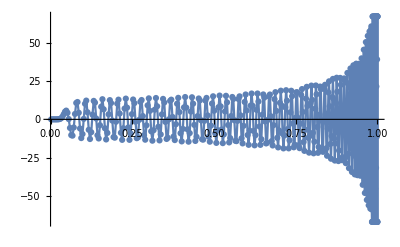

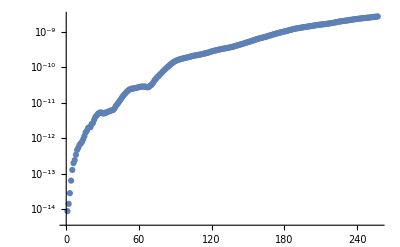

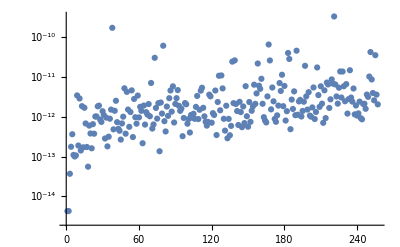

```mathematica
l = 13;
data = Import["worland_divrdiffr_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y^2 D[y^2 D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m(m+1)y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{5.65476×10^16,3.41061×10^-13,1.13687×10^-12,1.81899×10^-12,3.63798×10^-12,7.27596×10^-12,1.45519×10^-11,2.18279×10^-11,5.09317×10^-11,6.54836×10^-11,7.27596×10^-11,8.00355×10^-11,1.16415×10^-10,1.52795×10^-10,2.32831×10^-10,2.91038×10^-10,3.20142×10^-10,3.7835×10^-10,4.65661×10^-10,5.82077×10^-10,8.73115×10^-10,1.10595×10^-9,1.39698×10^-9,1.86265×10^-9,2.44472×10^-9,3.0268×10^-9,3.49246×10^-9,4.30737×10^-9,5.3551×10^-9,6.17001×10^-9,7.68341×10^-9,8.03266×10^-9,9.31323×10^-9,1.00117×10^-8,1.11759×10^-8,1.234×10^-8,1.30385×10^-8,1.35042×10^-8,1.5134×10^-8,1.67638×10^-8,1.81608×10^-8,1.93249×10^-8,2.16532×10^-8,2.30502×10^-8,2.6077×10^-8,2.77068×10^-8,2.98023×10^-8,3.1665×10^-8,3.25963×10^-8,3.49246×10^-8,3.86499×10^-8,4.37722×10^-8,4.93601×10^-8,5.58794×10^-8,6.51926×10^-8,7.82311×10^-8,9.12696×10^-8,1.08033×10^-7,1.24797×10^-7,1.41561×10^-7,1.61119×10^-7,1.78814×10^-7,1.98372×10^-7,2.16067×10^-7,2.38419×10^-7}

{1.,4.49978×10^-15,4.68012×10^-15,3.09743×10^-14,4.46251×10^-14,6.74011×10^-14,2.43062×10^-14,7.30867×10^-14,1.38647×10^-14,6.71627×10^-14,8.81884×10^-14,1.46507×10^-13,2.72294×10^-14,5.39826×10^-14,5.28728×10^-14,1.45454×10^-13,6.78446×10^-14,6.50635×10^-14,6.31064×10^-13,9.42709×10^-13,1.16029×10^-12,2.1494×10^-13,6.8552×10^-14,4.58806×10^-14,7.93586×10^-14,1.60023×10^-13,2.11892×10^-13,6.36223×10^-14,3.94502×10^-13,5.31392×10^-12,3.66273×10^-14,6.66078×10^-14,8.82612×10^-14,2.28976×10^-12,8.4402×10^-13,2.02831×10^-14,2.75762×10^-13,3.4674×10^-13,9.14725×10^-14,9.47659×10^-14,3.07171×10^-13,3.44641×10^-13,2.63759×10^-13,4.47914×10^-13,1.95907×10^-13,8.24045×10^-14,8.50527×10^-14,2.5183×10^-13,1.27639×10^-12,3.68696×10^-13,1.83998×10^-13,6.84627×10^-13,2.41192×10^-13,2.07657×10^-12,9.36401×10^-14,9.3192×10^-13,7.34933×10^-13,2.08247×10^-13,1.66617×10^-13,3.76481×10^-13,4.27256×10^-13,1.03517×10^-11,3.87038×10^-13,2.42874×10^-10,1.67355×10^-12}

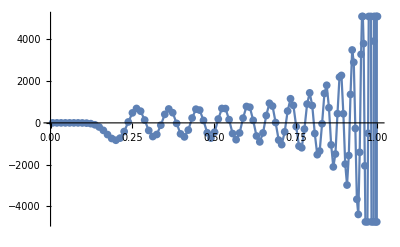

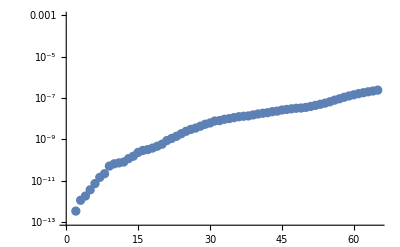

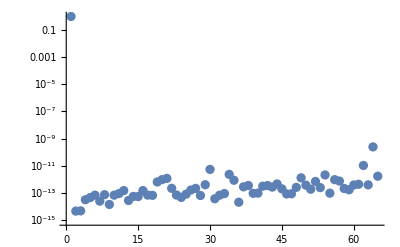

```mathematica
l = 13;
data = Import["worland_slapl_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{5.65476×10^16,2.27374×10^-13,9.09495×10^-13,2.27374×10^-12,3.63798×10^-12,5.45697×10^-12,1.63709×10^-11,3.63798×10^-11,4.72937×10^-11,7.27596×10^-11,8.73115×10^-11,8.00355×10^-11,1.16415×10^-10,1.38243×10^-10,2.03727×10^-10,2.76486×10^-10,3.20142×10^-10,3.49246×10^-10,4.07454×10^-10,5.23869×10^-10,7.567×10^-10,1.10595×10^-9,1.5134×10^-9,1.68802×10^-9,2.32831×10^-9,3.0268×10^-9,3.49246×10^-9,4.30737×10^-9,5.00586×10^-9,6.28643×10^-9,7.33417×10^-9,8.14907×10^-9,9.0804×10^-9,1.00117×10^-8,1.11759×10^-8,1.16415×10^-8,1.32713×10^-8,1.46683×10^-8,1.49012×10^-8,1.6531×10^-8,1.76951×10^-8,1.97906×10^-8,2.11876×10^-8,2.37487×10^-8,2.51457×10^-8,2.84053×10^-8,2.98023×10^-8,3.1665×10^-8,3.25963×10^-8,3.53903×10^-8,3.86499×10^-8,4.37722×10^-8,4.74975×10^-8,5.4948×10^-8,6.51926×10^-8,7.91624×10^-8,9.22009×10^-8,1.08965×10^-7,1.23866×10^-7,1.42492×10^-7,1.60187×10^-7,1.80677×10^-7,1.98372×10^-7,2.17929×10^-7,2.40281×10^-7}

{1.,4.78313×10^-15,4.45463×10^-15,1.92466×10^-14,3.2414×10^-14,3.42326×10^-14,1.48252×10^-14,2.1883×10^-13,2.85403×10^-14,8.24781×10^-14,2.38098×10^-13,1.29659×10^-13,1.44188×10^-13,5.78807×10^-14,2.87343×10^-14,1.34276×10^-13,1.39462×10^-14,3.77002×10^-13,1.36914×10^-13,1.62769×10^-14,8.39938×10^-14,2.92828×10^-13,5.11297×10^-14,3.32604×10^-14,1.6441×10^-13,1.56419×10^-13,2.14237×10^-13,6.33759×10^-14,5.34588×10^-14,1.13288×10^-12,3.61263×10^-13,2.13388×10^-13,8.92736×10^-14,9.67673×10^-14,1.1174×10^-12,2.00959×10^-14,3.2376×10^-13,8.62468×10^-13,8.90241×10^-14,1.13183×10^-13,3.18692×10^-12,2.62719×10^-13,8.72523×10^-14,9.91805×10^-13,1.97239×10^-13,3.7692×10^-13,2.42487×10^-13,5.13708×10^-13,7.69879×10^-13,1.85721×10^-13,1.47098×10^-13,1.88288×10^-13,2.64669×10^-13,3.00634×10^-13,1.13643×10^-13,1.15838×10^-12,1.64431×10^-13,4.70175×10^-13,1.65975×10^-13,1.90248×10^-13,4.38958×10^-13,5.57638×10^-13,3.86557×10^-13,7.45963×10^-11,3.19168×10^-12}

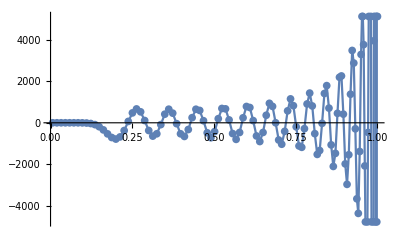

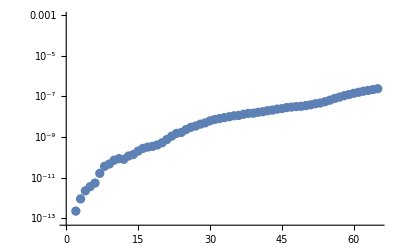

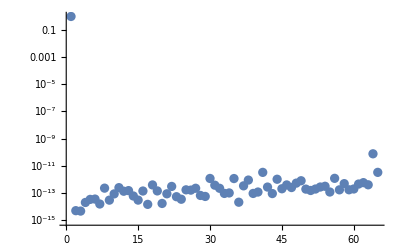

```mathematica
l = 13;
data = Import["worland_claplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
1/y^2 D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^3//Simplify
```

4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{8.7119×10^18,2.27374×10^-13,1.13687×10^-12,2.27374×10^-12,3.63798×10^-12,7.27596×10^-12,1.27329×10^-11,3.27418×10^-11,4.36557×10^-11,7.27596×10^-11,9.45874×10^-11,1.16415×10^-10,1.81899×10^-10,2.32831×10^-10,3.34694×10^-10,4.22006×10^-10,5.23869×10^-10,6.1118×10^-10,6.54836×10^-10,6.54836×10^-10,8.14907×10^-10,1.04774×10^-9,1.33878×10^-9,1.62981×10^-9,1.92085×10^-9,2.44472×10^-9,2.67755×10^-9,3.25963×10^-9,3.95812×10^-9,4.77303×10^-9,5.3551×10^-9,5.82077×10^-9,6.75209×10^-9,7.68341×10^-9,7.68341×10^-9,9.0804×10^-9,9.77889×10^-9,1.0943×10^-8,1.14087×10^-8,1.21072×10^-8,1.32713×10^-8,1.39698×10^-8,1.53668×10^-8,1.62981×10^-8,1.72295×10^-8,1.90921×10^-8,2.09548×10^-8,2.32831×10^-8,2.65427×10^-8,3.11993×10^-8,3.53903×10^-8,4.00469×10^-8,4.47035×10^-8,5.21541×10^-8,5.96046×10^-8,6.98492×10^-8,8.19564×10^-8,9.68575×10^-8,1.08033×10^-7,1.21072×10^-7,1.35042×10^-7,1.49943×10^-7,1.60187×10^-7,1.70432×10^-7,1.82539×10^-7}

{1.,4.44788×10^-15,4.56884×10^-15,3.14777×10^-14,2.93458×10^-14,3.8993×10^-14,1.21457×10^-14,1.78015×10^-13,4.97211×10^-14,7.76964×10^-14,3.41136×10^-13,1.52613×10^-13,9.64873×10^-14,5.21249×10^-14,3.88534×10^-14,1.53535×10^-13,1.48028×10^-14,6.64219×10^-13,2.54204×10^-13,6.17225×10^-14,5.17079×10^-14,1.62816×10^-13,5.35498×10^-14,3.45644×10^-14,3.67795×10^-13,2.75318×10^-13,8.18463×10^-14,4.1025×10^-14,1.59632×10^-13,8.07749×10^-13,3.05307×10^-13,6.71252×10^-14,3.13835×10^-14,8.43952×10^-14,1.17356×10^-12,3.24144×10^-14,5.82545×10^-13,8.8077×10^-13,1.53341×10^-13,1.14696×10^-13,2.03815×10^-12,1.29716×10^-13,1.56642×10^-13,1.77734×10^-12,3.02982×10^-13,1.31085×10^-13,2.05768×10^-13,6.72505×10^-13,7.26588×10^-13,2.61009×10^-13,9.15526×10^-14,1.5362×10^-13,1.96114×10^-13,8.80909×10^-13,1.0516×10^-13,1.20283×10^-12,1.0624×10^-13,8.92234×10^-13,1.95537×10^-13,1.74032×10^-13,8.695×10^-13,3.12513×10^-13,7.75633×10^-13,6.3625×10^-11,6.4168×10^-13}

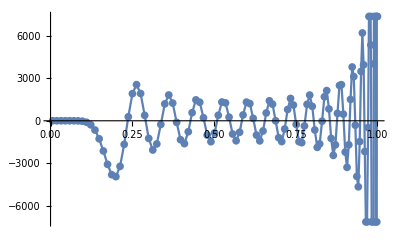

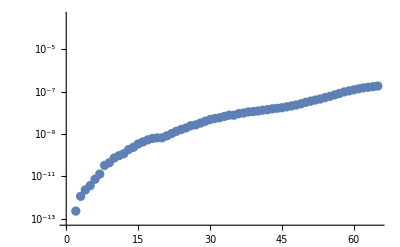

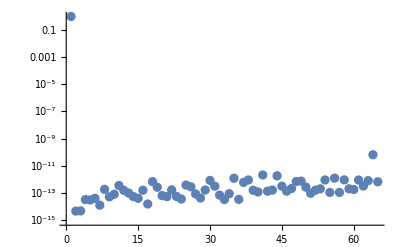

```mathematica
l = 13;
data = Import["worland_r_1claplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

```mathematica
D[1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2,{y,1}]//Simplify
```

4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{1.30678×10^20,9.7175×10^18,2.18279×10^-11,2926.25,2.32831×10^-10,5.82077×10^-10,2.09548×10^-9,2.32831×10^-9,3.72529×10^-9,6.51926×10^-9,1.11759×10^-8,1.86265×10^-8,2.23517×10^-8,5.58794×10^-8,8.9407×10^-8,9.68575×10^-8,1.2666×10^-7,1.93715×10^-7,3.12924×10^-7,4.47035×10^-7,5.96046×10^-7,8.64267×10^-7,1.3113×10^-6,1.84774×10^-6,2.563×10^-6,3.51667×10^-6,4.64916×10^-6,6.19888×10^-6,7.7486×10^-6,9.53674×10^-6,0.0000113249,0.0000140667,0.0000157356,0.0000190735,0.0000216961,0.0000255108,0.0000286102,0.0000333786,0.0000391006,0.0000448227,0.0000524521,0.0000619888,0.0000705719,0.0000801086,0.0000896454,0.000100136,0.000114441,0.000130653,0.000144958,0.000164032,0.000167847,0.000190735,0.000202179,0.000219345,0.000234604,0.000257492,0.000259399,0.000267029,0.000278473,0.000274658,0.000274658,0.000274658,0.000282288,0.000274658,0.000259399}

{1.,1.80901,4.75072×10^-15,3.75208,7.98011×10^-15,2.62408×10^-14,2.43655×10^-14,2.45692×10^-14,1.80679×10^-14,5.91929×10^-14,4.16324×10^-14,1.16639×10^-13,6.77439×10^-14,6.84434×10^-13,4.93124×10^-14,4.07758×10^-14,1.31004×10^-13,1.48071×10^-13,9.87208×10^-14,9.08206×10^-14,4.37967×10^-13,1.43351×10^-13,6.75041×10^-13,1.88863×10^-13,1.75541×10^-13,7.95214×10^-14,4.42909×10^-14,1.84458×10^-13,9.19205×10^-14,1.50238×10^-13,3.50768×10^-13,8.22246×10^-14,8.28732×10^-13,8.03584×10^-14,3.14985×10^-13,3.84238×10^-13,7.99968×10^-12,8.9195×10^-14,7.34764×10^-14,1.19825×10^-13,9.46009×10^-14,3.10923×10^-13,2.28125×10^-13,5.74188×10^-13,4.91249×10^-13,1.73937×10^-13,1.11845×10^-13,6.94449×10^-13,5.44792×10^-13,8.32448×10^-12,1.85074×10^-13,9.938×10^-14,2.16821×10^-13,4.62779×10^-13,1.26731×10^-13,3.07949×10^-13,2.38285×10^-13,9.33812×10^-13,9.61781×10^-14,3.65259×10^-13,6.86415×10^-13,2.1717×10^-13,1.37557×10^-13,4.93836×10^-13,6.89318×10^-13}

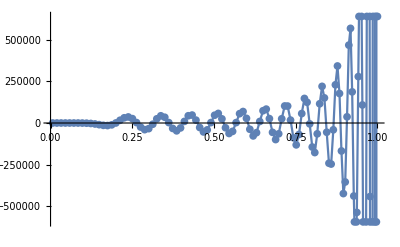

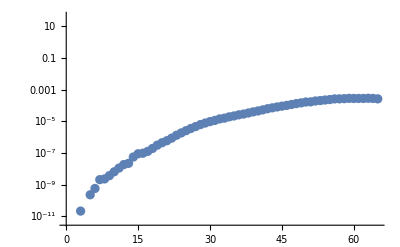

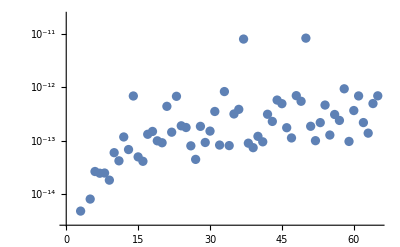

```mathematica
l = 13;
data = Import["worland_dclaplh_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
f[k_,m_,y_]=4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ √π\ √π\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ √π\ √π\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ √π\ √π\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{Indeterminate,0.333952,0.515737,0.613577,0.679332,0.721429,0.759095,0.779927,0.803066,0.827914,0.831015,0.853601,0.867615,0.877552,0.88288,0.878029,0.894557,0.909872,0.892172,0.919888,0.906848,0.929669,0.901832,0.939705,0.917706,0.928588,0.950316,0.919539,0.926221,0.95829,0.949707,0.894194,0.935526}

{Indeterminate,0.373343,0.536581,0.615753,0.664643,0.698645,0.724043,0.743944,0.760081,0.773508,0.784907,0.794742,0.803341,0.810943,0.817726,0.823828,0.829355,0.834393,0.83901,0.843261,0.847192,0.850841,0.854241,0.857419,0.860397,0.863196,0.865833,0.868324,0.870681,0.872915,0.875038,0.877057,0.878982}

-Graphics-

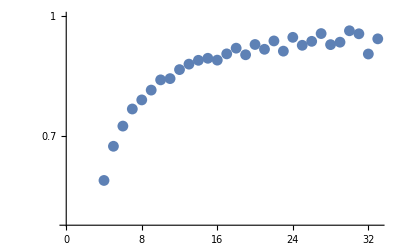

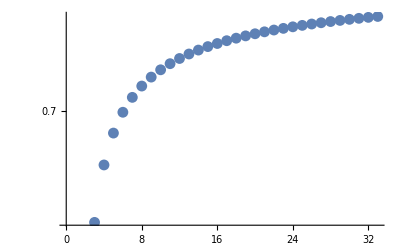

```mathematica
l = 13;
data = Import["worland_poly_l"<>ToString[l]<>".dat"];
x = data[[;;,1]];
α=-1/2;
β=k-1/2;
f[k_,m_,y_]=y^m JacobiP[k,-1/2,m-1/2,2 y^2-1]/√(1/(2k+α+β+1)(Gamma[k+α+1]Gamma[k+β+1])/(Gamma[k+α+β+1]Gamma[k+1]));
tmp = Table[Table[f[i,l,x[[j]]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}]
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}]
ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All]
ListLogPlot[error]
ListLogPlot[relError]
Clear[x]
Clear[tmp]
```